## Generalized Padé Approximation

Originally appeared in The Mathematica Journal 9(4).

It is often the case that, while an exact solution is difficult or impossible, series or asymptotic solutions to a particular problem can be obtained without too much difficulty. As is well known, Padé approximations (see mathworld.wolfram.com/PadeApproximant.html) are usually superior to Taylor expansions when functions contain poles, because the use of rational functions allows them to be well represented.

Define P_N(x) and Q_M(x) as polynomials of degrees N and M, with Q_M(0)=1.

```mathematica
P/:Subscript[P, n_]:=x↦∑_(i=0)^n Subscript[p, i] x^i
```

```mathematica
Q/:Subscript[Q, m_]:=x↦1+∑_(i=1)^m Subscript[q, i] x^i
```

The coefficients in the [N,M] Padé approximant to f(x) are determined by requiring that the Taylor expansion of f(x)-P_N(x)/Q_M(x) is of order O(x^(N+M+1)).

Suppose that you have obtained the following Taylor series up to O(x^5) for a function of interest.

```mathematica
taylor[x_]=1-(2 x)/3+(4 x^2)/15-(8 x^3)/105+(16 x^4)/945;
```

Here is the [2,2] Padé approximant for this series.

```mathematica
pade[x_]=PadeApproximant[taylor(x),{x,0,{2,2}}]
```

((32 x^2)/945-(2 x)/9+1)/((4 x^2)/63+(4 x)/9+1)

Verify that the Taylor expansion of f(x)-P_2(x)/Q_2(x) is of order O(x^5).

```mathematica
taylor[x]-pade[x]+O[x]^5
```

O(x^5)

A plot shows that the Taylor series diverges from the Padé approximant near x=1.

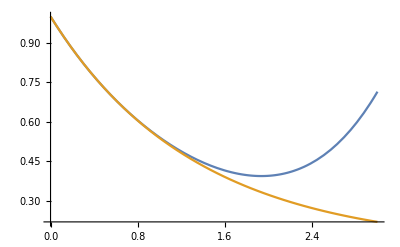

```mathematica
small=Plot[{Tooltip[taylor[x],"Taylor"],Tooltip[pade[x],"Padé"]},{x,0,3}]
```

Suppose now that you have also computed the following asymptotic series for the same function.

```mathematica
asymptotic[x_]=1/(2 x)+1/(4 x^2)+3/(8 x^3);
```

A plot shows that the Padé approximant about x=0 and the asymptotic expansion intersect at x≈2.5.

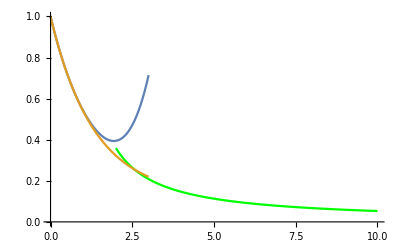

```mathematica
large=Show[{Plot[Tooltip[asymptotic(x),"Asymptotic"],{x,2,10},PlotStyle->Green],small},PlotRange->({{0, 10}, {0, 1}}),AxesOrigin->{0,0}]
```

How can you incorporate information from expansions of a function about two or more points? One approach is to generalize the idea of computing Padé approximants [Reference]. Suppose f(x) has the asymptotic expansions

f(x)∼∑_(i=0)^∞ a_i (x-x_0)^i, x→x_0,

f(x)∼∑_(i=0)^∞ b_i (x-x_1)^i, x→x_1,

in the neighborhoods of distinct points x_0 and x_1, respectively. To compute a two-point Padé approximant to f(x), we require that the rational function P_N(x)/Q_M(x) agrees with f(x) up to order J about x_0 and to order K about x_1, where J+K=N+M+1.

To use all the information at hand, note that for x_0=0, J=5, and for x_1=∞, K=4.

```mathematica
j=Exponent[taylor[x], x]+1
```

5

```mathematica
k=Exponent[asymptotic[x], 1/x]+1
```

4

The diagonal Padé approximant then has N=M=4.

```mathematica
n=m=1/2 (j+k-1)
```

4

It is straightforward to determine the coefficients p_i and q_i in terms of a_i and b_i. Here we obtain these coefficients using series arithmetic via SolveAlways.

```mathematica
SolveAlways[{taylor[x]-(Subscript[P, n](x))/(Subscript[Q, m](x))+O[x]^j==0,asymptotic[x]-(Subscript[P, n](x))/(Subscript[Q, m](x))+O[x,∞]^k==0},x]
```

{{p_0→1,p_1→2/9,p_2→52/945,p_3→8/945,q_2→8/21,p_4→0,q_1→8/9,q_3→32/315,q_4→16/945}}

Here is the two-point Padé approximant to f(x).

```mathematica
twopoint[x_]=(Subscript[P, n](x))/(Subscript[Q, m](x))/.First[%]
```

((8 x^3)/945+(52 x^2)/945+(2 x)/9+1)/((16 x^4)/945+(32 x^3)/315+(8 x^2)/21+(8 x)/9+1)

The two-point Padé approximant agrees with the Taylor series about x=0, the one-point Padé approximant about x=0, and the asymptotic expansion about x=∞.

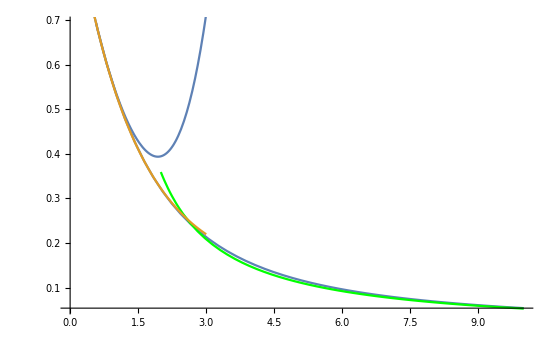

```mathematica
Show[Plot[Tooltip[twopoint(x),"Two-point Padé approximant"],{x,0,10}],large]
```

[Reference]  C. M. Bender and S. A. Orszag, Advanced Mathematical Methods for Scientists and Engineers, New York: McGraw-Hill, 1978, pp. 393–395.